# Simulation on SMWDC ray - tracking

## Raw Signal Generation

```mathematica
(* a paricle's travaling path *)
(* β = {x0, a, y0, b} *)
(* 3D Ray *)
Ray[β_,z_]:={β[[1]]+β[[2]]z,β[[3]]+β[[4]]z,z}
(* the {x,y} @ z=-40, z=40 *)
Bound[β_]:={Ray[β,-40][[1;;2]],Ray[β,40][[1;;2]]}
(* Normal of Ray *)
NormRay[β_]:=Normalize[(Ray[β,40]-Ray[β,-40])]
```

## MWDC Construction

```mathematica
(* plan angle *)
planθ[plan_]:=Switch[plan,
1,0,
2,0,
3,ArcCos[0.8],
4,ArcCos[0.8],
5,-ArcCos[0.8],
6,-ArcCos[0.8]
]
(* wire direction *)
wnorm[plan_]:={-Sin[planθ[plan]],Cos[planθ[plan]],0}
cell(*X,Y,Z*)={20,400,16};
firstwirePosition(*mm*)={0,5,13.125,9.5,13.125,9.5};
wstart[plan_,i_]:=
{(i-1)cell[[1]]/Cos[planθ[plan]]+firstwirePosition[[plan]],0,cell[[3]](plan-1)-40}
(* wire *)
w[plan_,i_,s_]:=wstart[plan,i]+s wnorm[plan]
(* number of wire *)
numWire[plan_]:=Switch[plan,
1,56,
2,56,
3,44,
4,44,
5,44,
6,44
]
(* Hightlight wire cell *)
Highlight[plane_,wire_,lis_]:=If[MemberQ[lis,{plane,wire,__}],0.5,0.1]
```

### chamber geometery drawing : MWDC2[β, size, α], MWDC2RaysFlat[k1_,k2_, size_, α_,plan_]

```mathematica
MWDC2[β_, size_, α_]:=Graphics3D[{
J=HitList[β];
fp=FirstPlan[J];
Ymin=Min[Ray[β,-60][[2]],Ray[β,60][[2]]]-20;
Ymax=Max[Ray[β,-60][[2]],Ray[β,60][[2]]]+20;
Corner1[plan_]:={-cell[[1]]/2,Ymin/Cos[planθ[plan]],-cell[[3]]/2};
Corner2[plan_]:={cell[[1]]/2,Ymax/Cos[planθ[plan]],cell[[3]]/2};
(*Z*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{0,0,100}}]},
(*X*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{40,0,0}}]},
(*Y*){Black,Arrow[{w[J[[1,1]],J[[1,2]],0],w[J[[1,1]],J[[1,2]],0]+{0,Ray[β,60][[2]]+50,0}}]},
{Red,Thickness[Large ],Arrow[{Ray[β,-60],Ray[β,60]}]},
Table[{Green,Opacity[Highlight[1,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[1,i]+Corner1[1],wstart[1,i]+Corner2[1]]},{i,J[[1,2]]-2,J[[1,2]]+2}],
Table[{Green,Opacity[Highlight[2,i,J]],EdgeForm[Opacity[α]],Cuboid[wstart[2,i]+Corner1[2],wstart[2,i]+Corner2[2]]},{i,J[[fp[[2]],2]]-2,J[[fp[[2]],2]]+2}],
Table[{Yellow,Opacity[Highlight[3,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[3,i]+Corner1[3],wstart[3,i]+Corner2[3]],-ArcSin[wnorm[3][[1]]],{0,0,1},wstart[3,i]]},{i,J[[fp[[3]],2]]-2,J[[fp[[3]],2]]+2}],
Table[{Yellow,Opacity[Highlight[4,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[4,i]+Corner1[4],wstart[4,i]+Corner2[4]],-ArcSin[wnorm[4][[1]]],{0,0,1},wstart[4,i]]},{i,J[[fp[[4]],2]]-2,J[[fp[[4]],2]]+2}],
Table[{Blue,Opacity[Highlight[5,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[5,i]+Corner1[5],wstart[5,i]+Corner2[5]],-ArcSin[wnorm[5][[1]]],{0,0,1},wstart[5,i]]},{i,J[[fp[[5]],2]]-2,J[[fp[[5]],2]]+2}],
Table[{Blue,Opacity[Highlight[6,i,J]],EdgeForm[Opacity[α]],Rotate[Cuboid[wstart[6,i]+Corner1[6],wstart[6,i]+Corner2[6]],-ArcSin[wnorm[6][[1]]],{0,0,1},wstart[6,i]]},{i,J[[fp[[6]],2]]-2,J[[fp[[6]],2]]+2}],
Table[{Red,Opacity[0.5],Cylinder[{w[J[[i,1]],J[[i,2]],(Ymin-20)/Cos[planθ[J[[i,1]]]]],w[J[[i,1]],J[[i,2]],(Ymax+20)/Cos[planθ[J[[i,1]]]]]},Abs[J[[i,5]]]]},{i,1,Length[J]}],
Text[J[[1,2]],w[J[[1,1]],J[[1,2]],0]+{-10,0,0}]
}, ImageSize->size]
MWDC2RaysFlat[k1_,k2_, size_, α_,plan_]:=(*ImageReflect[*)Graphics[{
J1=HitList[k1];
J2=HitList[k2];
fp1=FirstPlan[J1];
fp2=FirstPlan[J2];
(*Z*){Black,Arrow[{Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}],Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}]+{0,30}}]},
(*X*){Black,Arrow[{Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}],Drop[w[J1[[plan,1]],J1[[plan,2]],0],{2}]+{30,0}}]},
{Red,Thickness[Large ],Arrow[{Drop[Ray[k1,-50],{2}],Drop[Ray[k1,-10],{2}]}]},
{Blue,Thickness[Large ],Arrow[{Drop[Ray[k2,-50],{2}],Drop[Ray[k2,-10],{2}]}]},
Table[{Green,Opacity[0.2],EdgeForm[Opacity[α]],Rectangle[Drop[wstart[plan,i]-1/2 cell/{wnorm[plan][[2]],1,1},{2}],Drop[wstart[plan,i]+1/2 cell/{wnorm[plan][[2]],1,1},{2}]]},{i,J1[[fp1[[plan]],2]],J1[[fp1[[plan]],2]]+2}],
Table[{Green,Opacity[0.2],,EdgeForm[Opacity[α]],Rectangle[Drop[wstart[plan+1,i]-1/2 cell/{wnorm[plan+1][[2]],1,1},{2}],Drop[wstart[plan+1,i]+1/2 cell/{wnorm[plan+1][[2]],1,1},{2}]]},{i,J1[[fp1[[plan+1]],2]],J1[[fp1[[plan+1]],2]]+2}],
Table[{Red,
Circle[Drop[w[J1[[i,1]],J1[[i,2]],0],{2}],Abs[{J1[[i,5]]/(wnorm[plan][[2]]),J1[[i,5]]}]]},{i,fp1[[plan]],fp1[[plan+1]]+1}],
Table[{Blue,
Circle[Drop[w[J2[[i,1]],J2[[i,2]],0],{2}],Abs[{J2[[i,5]]/(wnorm[plan][[2]]),J2[[i,5]]}]]},{i,fp2[[plan]],fp2[[plan+1]]+1}],
Text[{J1[[1,2]],J1[[1,6]]-Crystal[1][[1]]},Drop[w[J1[[1,1]],J1[[1,2]],0]+{-5,0,0},{2}]]
}, ImageSize->size](*,Left->Right]*)
```

## Signal Construction

```mathematica
(* a shortest distance between 2 lines*) 
MaxDriftLen[plan_]:=Switch[plan,
1,10,
2,10,
3,10,
4,10,
5,10,
6,10
]
DriftLen[β_,plan_,i_]:={s,z,dl}/.Flatten[Solve[w[plan,i,s]+dl Normalize[Cross[wnorm[plan],NormRay[β]]]==Ray[β,z],{s,z,dl}]]
(* another method to calculate driftlenght *)
DriftLength[β_,plan_,i_]:=Abs[(wstart[plan,i]-Ray[β,0]).Normalize[Cross[wnorm[plan],NormRay[β]]]]
(* general 2 ray distance *)
Distance[ray1_,ray1Norm_,ray2_,ray2Norm_]:=Abs[(ray1-ray2).Normalize[Cross[ray1Norm,ray2Norm]]]
IncAng[β_]:=Module[{normβ,pβ},
normβ=NormRay[β];
Table[
(*pβ=Normalize[normβ-(normβ.wnorm[i])wnorm[i]];*)
(*pβ=normβ[[3]]/(√(1-(normβ.wnorm[i])^2));*)
pβ=1/(√(1+(β[[2]]Cos[planθ[i]]+β[[4]]Sin[planθ[i]])^2));
ArcCos[pβ]
,{i,1,6}]
]
HitList[β_]:= (* plane, wire, z, s, DL, wire Distance , Lz*)
Flatten[DeleteCases[Table[If[Abs[DriftLen[β,plan,i][[3]]]<MaxDriftLen[plan],
{plan,i,(plan-1)*cell[[3]]-40,DriftLen[β,plan,i][[1]],DriftLen[β,plan,i][[3]],Distance[wstart[plan,i],wnorm[plan],{0,0,0},{0,0,1}],Abs[(DriftLen[β,plan,i][[3]])/Cos[IncAng[β][[plan]]]]},0]
,{plan,1,6},{i,1,numWire[plan]}]
,0,2]
,1]
CountPlan[Lis_]:=Table[Count[Transpose[Lis][[1]],i],{i,1,6}];
(*FirstPlan[Lis_]:=Flatten[Table[Position[Lis,{i,__}][[1]],{i,1,6}]];*)
FirstPlan[Lis_]:=Flatten[Table[Position[Lis,{i,__}][[1]],{i,1,6}]];
LastPlan[Lis_]:=Table[Total[CountPlan[Lis][[1;;i]]],{i,1,6}];
ReducedFstHitList[β_]:=Module[{J,FstPlan},J=HitList[β];FstPlan=LastPlan[J];Table[J[[i]],{i,FstPlan}]]
ShortedHitList[β_]:=Module[{J,multi,FstPlan},J=HitList[β];multi=CountPlan[J];FstPlan=LastPlan[J];
DeleteCases[Table[If[multi[[i]]==0,0,If[multi[[i]]≠1 ,
If[Abs[ J[[FstPlan[[i]],5]]]<Abs[J[[FstPlan[[i]]-1,5]]],J[[FstPlan[[i]]]],J[[FstPlan[[i]]-1]]],
J[[FstPlan[[i]]]]
]],{i,6}],0,1]
]
```

## Target Ray Geometry

```mathematica
Crystal[mwdc_]:=Switch[mwdc,
(*1,{942.86,0,-1400}, Plastics*)
1,{390.36+552.5,0,-982.37},
2,{-390.36+552.5,0,-982.37}
]
(* norm Ray vector in mwdc frame, {θ,ϕ} = lab angle *)
Rayn[mwdc_,θ_,ϕ_]:=RotationMatrix[(-1)^mwdc π/3,{0,1,0}].{(-1)^(mwdc+1)Sin[θ °]Cos[ϕ °],(-1)^(mwdc+1)Sin[θ °]Sin[ϕ °],Cos[θ °]}
(* Ray from Crystal *)
RayC[mwdc_,θ_,ϕ_,s_]:=Crystal[mwdc]+s Rayn[mwdc,θ,ϕ]
Rayβ[mwdc_,θ_,ϕ_]:={
RayC[mwdc,θ,ϕ,s/.Flatten[Solve[RayC[mwdc,θ,ϕ,s][[3]]==0,s],1]][[1]],
Map[(#1[[1]])/(#1[[3]])&,{RayC[mwdc,θ,ϕ,100]-RayC[mwdc,θ,ϕ,0]}][[1]],
RayC[mwdc,θ,ϕ,s/.Flatten[Solve[RayC[mwdc,θ,ϕ,s][[3]]==0,s],1]][[2]],
Map[(#1[[2]])/(#1[[3]])&,{RayC[mwdc,θ,ϕ,100]-RayC[mwdc,θ,ϕ,0]}][[1]]}
```

## ReConstruction - Multi - Demension Regession

```mathematica
Binery[n_,digit_]:=If[Length[IntegerDigits[n,2]]<digit, 
Join[ Reverse[IntegerDigits[n,2]],Table[0,{i,1,digit-Length[IntegerDigits[n,2]]}]],
Reverse[IntegerDigits[n,2]]]
PossPos[J_,σ_,corr_]:=Module[{len,tran,bin},len=Length[J];tran=Transpose[J];
Table[bin=(-1)^Binery[i,len];tran[[6]]+bin (tran[[If[corr==1,7,5]]]+RandomVariate[NormalDistribution[0,σ],len]),{i,0,2^len-1}]
]
zpos[plane_]:=Switch[plane,
1,-40,
2,-24,
3,-8,
4,8,
5,24,
6,40]
```

```mathematica
h[z1_,z2_,z3_,z4_,z5_,z6_]:={
{Cos[planθ[1]],Cos[planθ[1]]z1,Sin[planθ[1]],Sin[planθ[1]]z1},
{Cos[planθ[2]],Cos[planθ[2]]z2,Sin[planθ[2]],Sin[planθ[2]]z2},
{Cos[planθ[3]] ,Cos[planθ[3]] z3,Sin[planθ[3]],Sin[planθ[3]]z3},
{ Cos[planθ[4]],Cos[planθ[4]] z4,Sin[planθ[4]],Sin[planθ[4]]z4},
{Cos[planθ[5]],Cos[planθ[5]] z5,Sin[planθ[5]],Sin[planθ[5]]z5},
{Cos[planθ[6]], Cos[planθ[6]]z6,Sin[planθ[6]],Sin[planθ[6]]z6}
}
h6=h[-40,-24,-8,8,24,40];
```

```mathematica
wstart[1,16]
```

{300,0,-40}

```mathematica
(* test *)
k=Rayβ[1,40,10];
MWDC2[k,600,0.1]
HitList[k]//TableForm
J=ShortedHitList[k];
J//TableForm
PosiYList=PossPos[J,0.001,1];
SSError=Table[{i,LinearModelFit[{h6,PosiYList[[i]]}]["ANOVATableEntries"][[-2,2]]},{i,1,64}];
SortedSSError=Sort[SSError,#1[[2]]<#2[[2]]&];
LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["ParameterConfidenceIntervalTable"]
LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}]["ANOVATable"]
Estβ=LinearModelFit[{h6,PosiYList[[SortedSSError[[1,1]]]]},{x0,a,y0,b}][{"BestFitParameters","ParameterErrors"}]
{k,Estβ[[1]],k-Estβ[[1]]}//TableForm
```

-Graphics3D-

1 | 31 | -40 | 112.632 | -7.67537 | 600 | 8.19063
2 | 30 | -24 | 114.905 | 0.795652 | 585 | 0.849066
3 | 27 | -8 | 143.612 | 3.39865 | 530.5 | 3.48443
4 | 27 | 8 | 146.498 | 2.69874 | 527.6 | 2.76686
5 | 20 | 24 | 144.759 | -7.97222 | 390.5 | 8.50023
6 | 19 | 40 | 159.186 | 7.95405 | 367.6 | 8.48086

1 | 31 | -40 | 112.632 | -7.67537 | 600 | 8.19063
2 | 30 | -24 | 114.905 | 0.795652 | 585 | 0.849066
3 | 27 | -8 | 143.612 | 3.39865 | 530.5 | 3.48443
4 | 27 | 8 | 146.498 | 2.69874 | 527.6 | 2.76686
5 | 20 | 24 | 144.759 | -7.97222 | 390.5 | 8.50023
6 | 19 | 40 | 159.186 | 7.95405 | 367.6 | 8.48086

| Estimate | Standard Error | Confidence Interval
x0 | 576.909 | 0.00107163 | {576.904,576.913}
a | -0.372508 | 0.0000341685 | {-0.372655,-0.372361}
y0 | 117.749 | 0.0016995 | {117.741,117.756}
b | 0.11988 | 0.000115066 | {0.119385,0.120375}

| DF | SS | MS | F-Statistic | P-Value
x0 | 1 | 1.52334×10^6 | 1.52334×10^6 | 1.05991×10^12 | 9.43468×10^-13
a | 1 | 7273.85 | 7273.85 | 5.06102×10^9 | 1.97589×10^-10
y0 | 1 | 16636.2 | 16636.2 | 1.15752×10^10 | 8.63917×10^-11
b | 1 | 1.56 | 1.56 | 1.08542×10^6 | 9.21302×10^-7
Error | 2 | 2.87446×10^-6 | 1.43723×10^-6 |  | 
Total | 6 | 1.54725×10^6 |  |  |

{{576.909,-0.372508,117.749,0.11988},{0.00107163,0.0000341685,0.0016995,0.000115066}}

576.909 | -0.372519 | 117.748 | 0.119861
576.909 | -0.372508 | 117.749 | 0.11988
-0.000229947 | -0.0000111119 | -0.000834849 | -0.0000185261

## ReConstruction - Reverse Function

```mathematica
β={X,A,Y,B};
k=FullSimplify[NormRay[β],{A,B}>0]
r={X,Y,0};
wn={-Sin[θ],Cos[θ],0};
rw={wx,0,z0};
(r-rw).FullSimplify[Normalize[Cross[wn,k]],{1+A^2+B^2, Cos[θ],Sin[θ]}>0]
```

{A/(√(1+A^2+B^2)),B/(√(1+A^2+B^2)),1/(√(1+A^2+B^2))}

((-wx+X) Cos[θ])/(√((1+A^2) Cos[θ]^2+(1+B^2) Sin[θ]^2+A B Sin[2 θ]))+(Y Sin[θ])/(√((1+A^2) Cos[θ]^2+(1+B^2) Sin[θ]^2+A B Sin[2 θ]))-(z0 (-A Cos[θ]-B Sin[θ]))/(√((1+A^2) Cos[θ]^2+(1+B^2) Sin[θ]^2+A B Sin[2 θ]))

```mathematica
Simplify[(√(1-(k.wn)^2))/k[[3]],{1+A^2+B^2, Cos[θ],Sin[θ]}>0]
```

√(1+A^2+B^2-B^2 Cos[θ]^2-A^2 Sin[θ]^2+A B Sin[2 θ])

```mathematica
FullSimplify[(1+A^2) Cos[θ]^2+(1+B^2) Sin[θ]^2+A B Sin[2 θ]-(1+A^2+B^2-B^2 Cos[θ]^2-A^2 Sin[θ]^2+A B Sin[2 θ])]
```

0

```mathematica
(* the set of eqaution for DriftLength l *)
((-wx+X) Cos[θ])/(√(1+(A Cos[θ]+B Sin[θ])^2))+(Y Sin[θ])/(√(1+(A Cos[θ]+B Sin[θ])^2))+(z0 (A Cos[θ]+B Sin[θ]))/(√(1+(A Cos[θ]+B Sin[θ])^2))==l
```

```mathematica
(* (A Cos[θ]+B Sin[θ]) = ξ *)
1/(√(1+ξ^2))((-wx+X) Cos[θ]+Y Sin[θ]+z0 ξ) ==l
X Cos[θ]+Y Sin[θ]+z0 ξ - √(1+ξ^2) l ==wx Cos[θ]
(* Solve for X, Y, ξ=A Cos[θ]+B Sin[θ], ζ=√(1+ξ^2) *)
```

```mathematica
((-wx+X) Cos[θ])/(√(1+(A Cos[θ]+B Sin[θ])^2))+(Y Sin[θ])/(√(1+(A Cos[θ]+B Sin[θ])^2))+(z0 (A Cos[θ]+B Sin[θ]))/(√(1+(A Cos[θ]+B Sin[θ])^2))/.{wx->wstart[J[[4,1]],J[[4,2]]][[1]],θ->planθ[4],X->k[[1]],Y-> k[[3]],A->k[[2]],B-> k[[4]],z0-> zpos[4]}
```

-1.61701

```mathematica
(*test *)
k
J//TableForm
```

{576.909,-0.372519,117.748,0.119861}

1 | 31 | -40 | 112.632 | -7.67537 | 600 | 8.19063
2 | 30 | -24 | 114.905 | 0.795652 | 585 | 0.849066
3 | 27 | -8 | 143.612 | 3.39865 | 530.5 | 3.48443
4 | 27 | 8 | 146.498 | 2.69874 | 527.6 | 2.76686
5 | 20 | 24 | 144.759 | -7.97222 | 390.5 | 8.50023
6 | 19 | 40 | 159.186 | 7.95405 | 367.6 | 8.48086

```mathematica
DL={7.93609667,5.18,0.5078,5.235,0.6856,5.277};
wpos={-742.86,-757.86,-619.7879,-624.7879,-639.7879,-644.7879};
sign={1,1,-1,-1,-1,-1}
F1=Solve[{X-40 A==sign[[1]]DL[[1]] √(1+A^2)+wpos[[1]],
X-24A== sign[[2]]DL[[2]] √(1+A^2)+wpos[[2]]},{A,X}][[1]];
F2=Solve[
Table[(X Cos[planθ[i]]+A zpos[i]Cos[planθ[i]]+Y Sin[planθ[i]]+B zpos[i] Sin[planθ[i]]==sign[[i]]DL[[i]] √(1+(A Cos[planθ[i]]+B Sin[planθ[i]])^2)+wpos[[i]])/.F1,{i,5,6}],{Y,B}][[1]];
{X,A,Y,B}/.F1/.F2
```

{1,1,-1,-1,-1,-1}

{-778.72,-1.20758,3.16025,-0.517367}

```mathematica
MWDC2[{-781.7211+Crystal[1][[1]],-0.726182,0.23,-0.308545},500,0.2]
J//TableForm
```

-Graphics3D-

1 | 10 | -40 | 11.0775 | 8.24221 | 180 | 10.1862
1 | 11 | -40 | 14.0115 | -7.94091 | 200 | 9.81382
2 | 10 | -24 | 8.57876 | -5.20508 | 185 | 6.43273
3 | 7 | -8 | 0.291187 | 3.71332 | 130.5 | 4.6777
4 | 7 | 8 | 0.284972 | -3.71472 | 127.6 | 4.67946
5 | 6 | 24 | -4.43797 | 8.15767 | 110.5 | 8.77347
6 | 6 | 40 | -12.3818 | 4.96554 | 107.6 | 5.34038

```mathematica
J1//TableForm
```

1 | 31 | -40 | 0. | 8.62449 | 600 | 9.14928
2 | 31 | -24 | 0. | -1.42963 | 605 | 1.51662
3 | 24 | -8 | -5.38344 | 7.4604 | 470.5 | 7.75399
4 | 24 | 8 | -4.24988 | 5.8895 | 467.6 | 6.12127
5 | 24 | 24 | -0.910511 | -1.26179 | 470.5 | 1.31145
6 | 24 | 40 | -2.04407 | -2.83269 | 467.6 | 2.94416

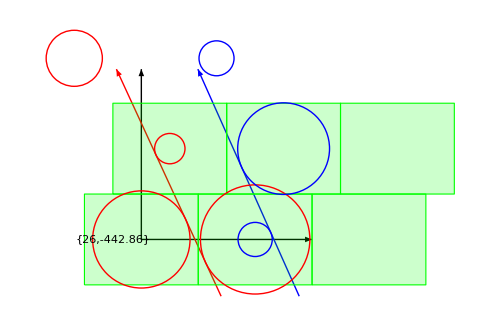

```mathematica
MWDC2RaysFlat[Rayβ[1,35.3,0],Rayβ[1,36,0],500,1,1]
```

```mathematica
F1=Solve[Table[X Cos[planθ[i]]+A zpos[i]Cos[planθ[i]]+Y Sin[planθ[i]]+B zpos[i] Sin[planθ[i]]==DL[[i]] √(1+(A Cos[planθ[i]]+B Sin[planθ[i]])^2)+wpos[[i]],{i,1,2}],{X,A}][[1]];
F2=Solve[Table[(X Cos[planθ[i]]+A zpos[i]Cos[planθ[i]]+Y Sin[planθ[i]]+B zpos[i] Sin[planθ[i]]==DL[[i]] √(1+(A Cos[planθ[i]]+B Sin[planθ[i]])^2)+wpos[[i]])/.F1,{i,3,4}],{Y,B}][[1]];
({X,A,Y,B}/.F1)/.F2
```

{-1824.25,-56.639,1399.94,75.4877}

```mathematica
(* generate the DL combination *)
PossDL[J_]:=Table[ ((-1)^Binery[i,6])Transpose[J][[5]],{i,0,2^6-1}]
```

```mathematica
DL=PossDL[J];
DLref=Abs[Transpose[J][[5]]]
```

{7.67537,0.795652,3.39865,2.69874,7.97222,7.95405}

```mathematica
Possβ=Table[F1=Solve[Table[X Cos[planθ[i]]+A zpos[i]Cos[planθ[i]]+Y Sin[planθ[i]]+B zpos[i] Sin[planθ[i]]==DL[[j,i]] √(1+(A Cos[planθ[i]]+B Sin[planθ[i]])^2)+J[[i,6]],{i,1,2}],{X,A}][[1]];
F2=Solve[Table[(X Cos[planθ[i]]+A zpos[i]Cos[planθ[i]]+Y Sin[planθ[i]]+B zpos[i] Sin[planθ[i]]==DL[[j,i]] √(1+(A Cos[planθ[i]]+B Sin[planθ[i]])^2)+J[[i,6]])/.F1,{i,3,4}],{Y,B}][[1]];
({X,A,Y,B}/.F1)/.F2,{j,1,2^6}];
```

```mathematica
k
Possβ[[1]]
```

{576.909,-0.372519,117.748,0.119861}

{576.909,-0.372519,117.748,0.119861}

```mathematica
(* using Possβ to regerate DL at 5 or 6 plan and check the difference *)
PossError=Monitor[Table[{j,Norm[Abs[Transpose[ShortedHitList[Possβ[[j]]]][[5,5;;6]]]-DLref[[5;;6]]]},{j,1,2^6}],j];
```

```mathematica
SortedPossError=Sort[PossError,#1[[2]]<#2[[2]]&];
```

```mathematica
PossError[[1;;10]]
SortedPossError[[1;;10]]
```

{{1,1.30502×10^-13},{2,11.1387},{3,7.98713},{4,9.11996},{5,5.78982},{6,8.5743},{7,7.43611},{8,10.7031},{9,4.05418},{10,9.05734}}

{{49,1.30502×10^-13},{33,1.30502×10^-13},{17,1.30502×10^-13},{1,1.30502×10^-13},{61,3.9445},{45,3.9445},{29,3.9445},{13,3.9445},{59,3.99446},{43,3.99446}}

```mathematica
Possβ[[33]]
k
Abs[Transpose[ShortedHitList[Possβ[[33]]]][[5]]]
DLref
```

{576.909,-0.372519,117.748,0.119861}

{576.909,-0.372519,117.748,0.119861}

{7.67537,0.795652,3.39865,2.69874,7.97222,7.95405}

{7.67537,0.795652,3.39865,2.69874,7.97222,7.95405}

```mathematica
Solve[{X-40 A== L1 √(1+A^2)+W1,
X-24A== L2 √(1+A^2)+W2},{A,X}]//FullSimplify
```

{{A→-(-16 W1+√(-(L1-L2)^2 (-256+(L1-L2)^2-(W1-W2)^2))+16 W2)/(-256+(L1-L2)^2),X→(384 W1)/(-256+(L1-L2)^2)-(24 √(-(L1-L2)^2 (-256+(L1-L2)^2-(W1-W2)^2)))/(-256+(L1-L2)^2)+W2-(384 W2)/(-256+(L1-L2)^2)+1/2 L2 √(4+(4 (-16 W1+√(-(L1-L2)^2 (-256+(L1-L2)^2-(W1-W2)^2))+16 W2)^2)/((-256+(L1-L2)^2)^2))},{A→(16 W1+√(-(L1-L2)^2 (-256+(L1-L2)^2-(W1-W2)^2))-16 W2)/(-256+(L1-L2)^2),X→(384 W1)/(-256+(L1-L2)^2)+1/2 L2 √(4+(4 (16 W1+√(-(L1-L2)^2 (-256+(L1-L2)^2-(W1-W2)^2))-16 W2)^2)/((-256+(L1-L2)^2)^2))+(24 √(-(L1-L2)^2 (-256+(L1-L2)^2-(W1-W2)^2)))/(-256+(L1-L2)^2)+W2-(384 W2)/(-256+(L1-L2)^2)}}

```mathematica
-(-16 W1+√(-(L1-L2)^2 (-256+(L1-L2)^2-(W1-W2)^2))+16 W2)/(-256+(L1-L2)^2)/.{W1->W2+ΔW,L1->L2+ΔL}//Simplify
```

(16 ΔW-√(-ΔL^2 (-256+ΔL^2-ΔW^2)))/(-256+ΔL^2)

```mathematica
Solve[{Y s-8H  ==L3 √(1+H^2)+W3,
Y s+H 8 ==L4 √(1+H^2)+W4},{Y,H}]//Simplify
```

{{Y→1/s(-(128 W3)/(-256+L3^2-2 L3 L4+L4^2)+W4+(128 W4)/(-256+L3^2-2 L3 L4+L4^2)+(8 √(-(L3-L4)^2 (-256+L3^2-2 L3 L4+L4^2-W3^2+2 W3 W4-W4^2)))/(-256+L3^2-2 L3 L4+L4^2)+1/2 L4 √(4+(4 (-16 W3+16 W4+√(-(L3-L4)^2 (-256+L3^2-2 L3 L4+L4^2-W3^2+2 W3 W4-W4^2)))^2)/((-256+L3^2-2 L3 L4+L4^2)^2))),H→-(-16 W3+16 W4+√(-(L3-L4)^2 (-256+L3^2-2 L3 L4+L4^2-W3^2+2 W3 W4-W4^2)))/(-256+L3^2-2 L3 L4+L4^2)},{Y→1/s(-(128 W3)/(-256+L3^2-2 L3 L4+L4^2)+W4+(128 W4)/(-256+L3^2-2 L3 L4+L4^2)-(8 √(-(L3-L4)^2 (-256+L3^2-2 L3 L4+L4^2-W3^2+2 W3 W4-W4^2)))/(-256+L3^2-2 L3 L4+L4^2)+1/2 L4 √(4+(4 (16 W3-16 W4+√(-(L3-L4)^2 (-256+L3^2-2 L3 L4+L4^2-W3^2+2 W3 W4-W4^2)))^2)/((-256+L3^2-2 L3 L4+L4^2)^2))),H→(16 W3-16 W4+√(-(L3-L4)^2 (-256+L3^2-2 L3 L4+L4^2-W3^2+2 W3 W4-W4^2)))/(-256+L3^2-2 L3 L4+L4^2)}}

```mathematica
-(-16 W3+16 W4+√(-(L3-L4)^2 (-256+L3^2-2 L3 L4+L4^2-W3^2+2 W3 W4-W4^2)))/(-256+L3^2-2 L3 L4+L4^2)/.{W4->W3+ΔW,L4->L3+ΔL}//Simplify
```

(16 ΔW+√(-ΔL^2 (-256+ΔL^2-ΔW^2)))/(256-ΔL^2)